```mathematica
∫_(x/10)^10 ((10-r)  (10-x/r))/(50*50*r)ⅆr
```

ConditionalExpression[(2 (-100+x+(100+x) Log[10])-(100+x) Log[x])/2500,(x∉Reals||0<Re[x]<100||Re[x]>100)&&(x/(-100+x)∉Reals||Re[x/(-100+x)]≥1||Re[x/(-100+x)]≤0)]

```mathematica
∫_0.1^(s-0.1) (10r-1)(10(s-r)-1)/(50r^3*50(s-r)^3)ⅆr
```

ConditionalExpression[1/2500(-(1. (-0.138155+3.54465 s-31.0517 s^2+100.259 s^3-10.517 s^4-500. s^5+(-0.06+1.8 s-20. s^2+100. s^3-200. s^4) Log[0.1-1. s]))/((0.1-1. s)^2 s^5)+1/((-0.1+s)^2 s^5)((0.138155-0.188496 ⅈ)-(3.54465-5.65487 ⅈ) s+(31.0517-62.8319 ⅈ) s^2-(100.259-314.159 ⅈ) s^3+(10.517-628.319 ⅈ) s^4+500. s^5+(0.06-1.8 s+20. s^2-100. s^3+200. s^4) Log[-0.1+s])),(s∉Reals||Re[s]≥0.1)&&((Re[(-0.1+s)/(-0.2+s)]≥1&&((0.1-1. s)/(-0.2+s)∉Reals||Re[(0.1-1. s)/(0.2-1. s)]≥1||Re[(0.1-1. s)/(-0.2+s)]==-1))||(-0.1+s)/(-0.2+s)∉Reals||Re[(-0.1+s)/(-0.2+s)]≤0)]

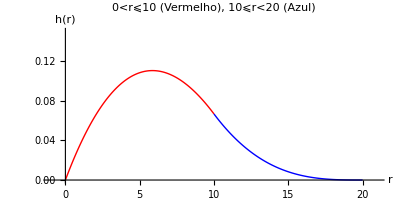

```mathematica
Show[
Plot[0,{r,-1,21},PlotStyle->{Opacity[0]}, PlotRange->{-0,.15},AxesLabel->{r,"h(r)"},GridLines->{{10,20},{4/15 (√2-1)}},PerformanceGoal->"Quality",AspectRatio->.5,PlotPoints->2000, PlotLabel->"0<r⩽10 (Vermelho), 10⩽r<20 (Azul)"],
Plot[{r(r^2-60r+600)/15000 },{r,0,10},PlotPoints->2000, PlotStyle->Red],
Plot[{-(r-20)^3/15000},{r,10,20},PlotPoints->2000, PlotStyle->Blue]
]
```

```mathematica
∫_a^(s-a) a^2/(x^2*(s-a)^2)ⅆx
```

ConditionalExpression[(a^2 (1/a+1/(a-s)))/(a-s)^2,(2 a^2≠a s&&Re[a/(-2 a+s)]≥0)||Re[a/(-2 a+s)]==-1||Re[a/(2 a-s)]≥1||a/(-2 a+s)∉Reals]